```mathematica
ResourceFunction["MaTeXInstall"][]
```

$Aborted

```mathematica
<<MaTeX`
```

```mathematica
data = Import["/Users/apatron/Desktop/codes/metropolis/numerical diagonalisation/eigenvector_alphaa.dat"];
data2 = Import["/Users/apatron/Desktop/codes/metropolis/numerical diagonalisation/eigenvector_musigma.dat"];
data3 = Import["/Users/apatron/Desktop/codes/metropolis/numerical diagonalisation/eigenvector_ab.dat"];
```

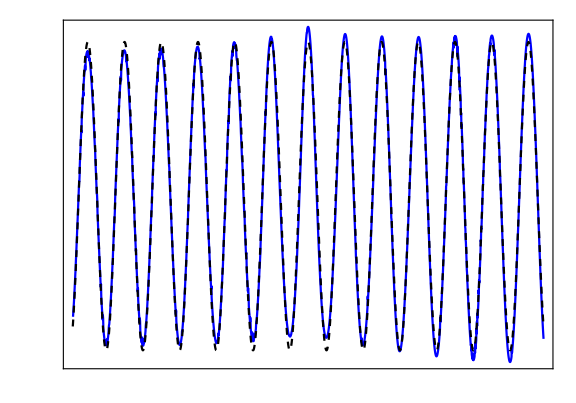

```mathematica
Gauss[x_]:=Exp[-x^2/4]/(2*Pi)^(1/4);

xvec = data[[All,1]];
yvec=data[[All,2]]/Exp[-xvec^2/4]*(Pi/2)^(1/4)*(1 + Exp[-2*(2*Pi/1.86)^2]);
yvec2=data[[All,2]];

xvec3 = data2[[All,1]];
yvec3=-data2[[All,2]]/Exp[-xvec^2/4]*(Pi/2)^(1/4)*(1 + Exp[-2*(2*Pi/1.8)^2]);
datavec3 = Transpose@{xvec3,yvec3};
datavecflip=Transpose@{xvec,-yvec2};
datavec = Transpose@{xvec,-yvec};
datavec2 = Transpose@{xvec,-data2[[All,2]]};

p1=Show[ListLinePlot[datavec,PlotStyle->Blue,PlotRange->All],Plot[Cos[2*Pi*x/1.56],{x,-10,10},PlotStyle->{Black,Dashed}],Frame->True,FrameStyle->Directive[Black,28,FontFamily->"Times New Roman"],FrameLabel->MaTeX[{"x","\\psi_1/\\psi_0"},Magnification->1],ImageSize->Large,AspectRatio->0.7,PlotRange->Full,FrameTicks->{{Table[{0.5*i,MaTeX[NumberForm[0.5*i,{2,1}],Magnification->1]},{i,-3,3}],None},{Table[{5*i,MaTeX[NumberForm[5*i,{2,1}],Magnification->1]},{i,-3,3}],None}}]
```

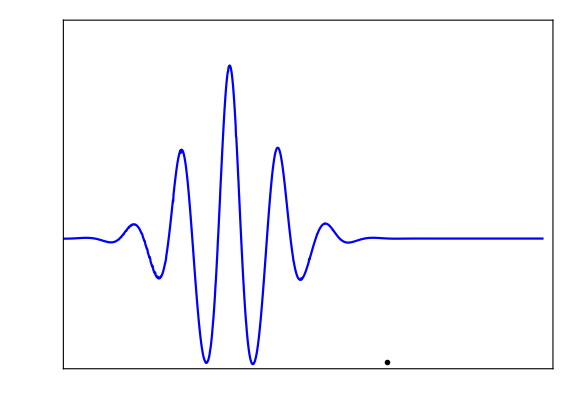

```mathematica
p2=Show[ListLinePlot[datavecflip,PlotStyle->Blue,PlotRange->All],Frame->True,FrameStyle->Directive[Black,28,FontFamily->"Times New Roman"],FrameLabel->MaTeX[{"x","\\psi_1"},Magnification->2],ImageSize->Large,AspectRatio->0.7,PlotRange->{{-5,10},{-0.7,1.2}},FrameTicks->{{Table[{0.5*i,MaTeX[NumberForm[0.5*i,{2,1}],Magnification->2]},{i,-3,3}],None},{Table[{5*i,MaTeX[NumberForm[5*i,{2,1}],Magnification->2]},{i,-3,3}],None}},Epilog->Inset[MaTeX["\\omega(\\eta) = \\omega^{(\\alpha,a)}(\\eta)",Magnification->2],{5,-0.7},Scaled[{0.125,0.05}]]]
```

```mathematica
Show[p2,Graphics@Inset[p1,{5.85,0.69},Automatic,Scaled[0.57]]]
```

-Graphics-
-Graphics-

```mathematica
x = data3[[All,1]];
y2=data3[[All,2]]/Exp[-x^2/4]*(Pi/2)^(1/4)*(1 + Exp[-2*(2*Pi/1.61)^2]);
dataGaus1=Transpose@{x,data3[[All,2]]};
dataGaus2=Transpose@{x,y2};
```

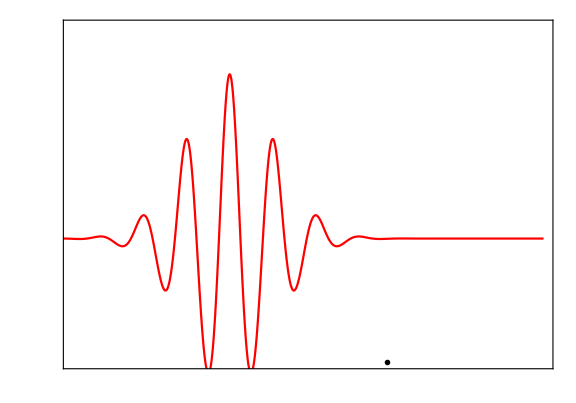

```mathematica
p2gaus=Show[ListLinePlot[dataGaus1,PlotStyle->Red,PlotRange->All],Frame->True,FrameStyle->Directive[Black,28,FontFamily->"Times New Roman"],FrameLabel->MaTeX[{"x","\\psi_1"},Magnification->2],ImageSize->Large,AspectRatio->0.7,PlotRange->{{-5,10},{-0.7,1.2}},FrameTicks->{{Table[{0.5*i,MaTeX[NumberForm[0.5*i,{2,1}],Magnification->2]},{i,-3,3}],None},{Table[{5*i,MaTeX[NumberForm[5*i,{2,1}],Magnification->2]},{i,-3,3}],None}},Epilog->Inset[MaTeX["\\omega(\\eta) = \\omega^{(a,\\sigma)}(\\eta)",Magnification->2],{5,-0.7},Scaled[{0.125,0.05}]]]
```

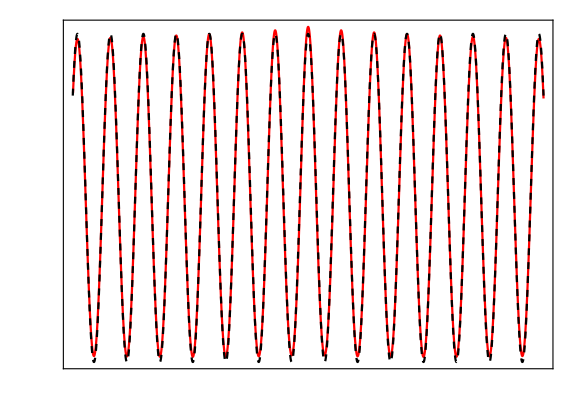

```mathematica
p1Gaus=Show[ListLinePlot[dataGaus2,PlotStyle->Red,PlotRange->All],Plot[Cos[2*Pi*x/1.4],{x,-10,10},PlotStyle->{Black,Dashed}],Frame->True,FrameStyle->Directive[Black,28,FontFamily->"Times New Roman"],FrameLabel->MaTeX[{"x","\\psi_1/\\psi_0"},Magnification->1],ImageSize->Large,AspectRatio->0.7,PlotRange->Full,FrameTicks->{{Table[{0.5*i,MaTeX[NumberForm[0.5*i,{2,1}],Magnification->1]},{i,-3,3}],None},{Table[{5*i,MaTeX[NumberForm[5*i,{2,1}],Magnification->1]},{i,-3,3}],None}}]
```

```mathematica
Show[p2gaus,Graphics@Inset[p1Gaus,{5.85,0.69},Automatic,Scaled[0.57]]]
```

-Graphics-
-Graphics-

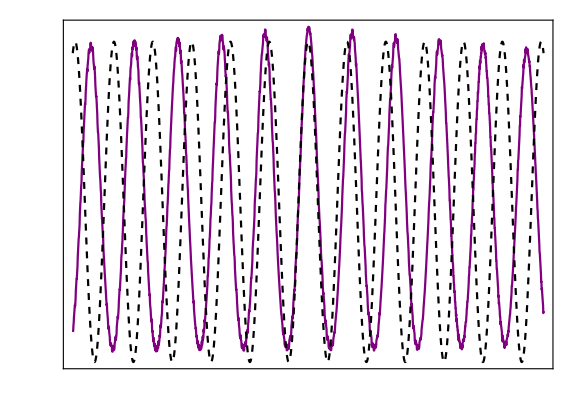

```mathematica
p1=Show[ListLinePlot[datavec3,PlotStyle->Purple,PlotRange->All],Plot[Cos[2*Pi*x/1.65],{x,-10,10},PlotStyle->{Black,Dashed}],Frame->True,FrameStyle->Directive[Black,28,FontFamily->"Times New Roman"],FrameLabel->MaTeX[{"x","\\psi_1/\\psi_0"},Magnification->1],ImageSize->Large,AspectRatio->0.7,PlotRange->Full,FrameTicks->{{Table[{0.5*i,MaTeX[NumberForm[0.5*i,{2,1}],Magnification->1]},{i,-3,3}],None},{Table[{5*i,MaTeX[NumberForm[5*i,{2,1}],Magnification->1]},{i,-3,3}],None}}]
```

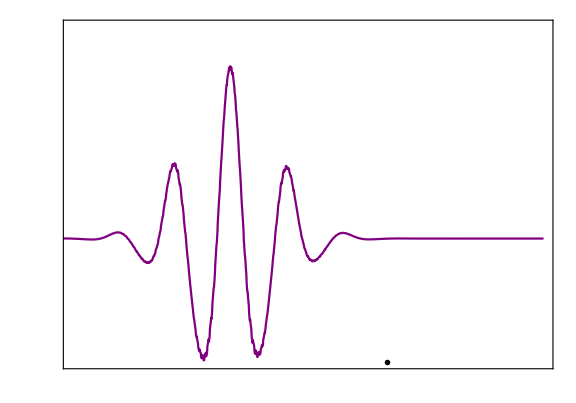

```mathematica
p2=Show[ListLinePlot[datavec2,PlotStyle->Purple,PlotRange->All],Frame->True,FrameStyle->Directive[Black,28,FontFamily->"Times New Roman"],FrameLabel->MaTeX[{"x","\\psi_1"},Magnification->2],ImageSize->Large,AspectRatio->0.7,PlotRange->{{-5,10},{-0.7,1.2}},FrameTicks->{{Table[{0.5*i,MaTeX[NumberForm[0.5*i,{2,1}],Magnification->2]},{i,-3,3}],None},{Table[{5*i,MaTeX[NumberForm[5*i,{2,1}],Magnification->2]},{i,-3,3}],None}},Epilog->Inset[MaTeX["\\omega(\\eta) = \\omega^{(a,b)}(\\eta)",Magnification->2],{5,-0.7},Scaled[{0.125,0.05}]]]
```

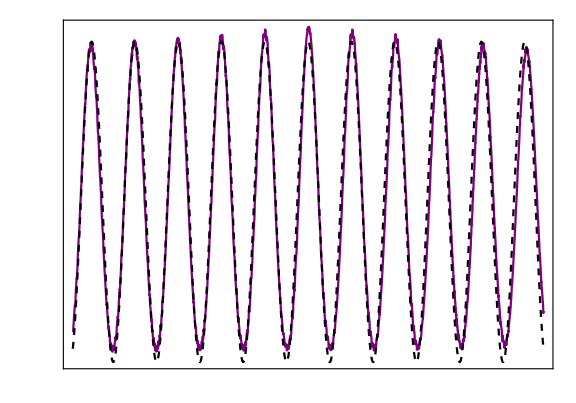
-Graphics-
-Graphics-

```mathematica
Show[p2,Graphics@Inset[p1,{5.85,0.69},Automatic,Scaled[0.57]]]
```

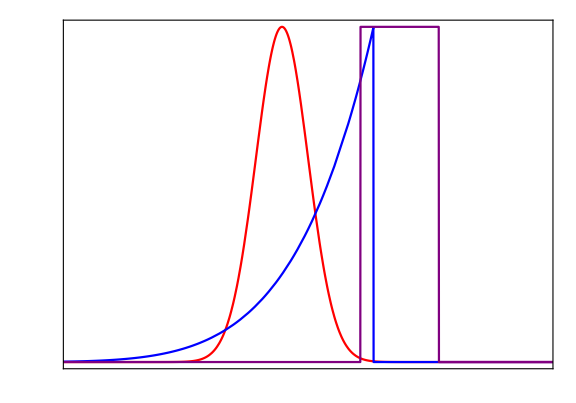

```mathematica
w1[x_,mu_,sigma_]:=Exp[-0.5*(x-mu)^2/sigma^2];
w2[x_,alpha_,a_]:=x^(alpha)*HeavisideTheta[a-x]/a^(alpha);
w3[x_,a_,b_]:=HeavisideTheta[x-b]*HeavisideTheta[a-x];

Show[Plot[w1[x,1.4,0.1],{x,0,2.7},PlotRange->All,PlotStyle->Red],Plot[w2[x,6,1.75],{x,0,2.7},PlotRange->All,PlotStyle->Blue,Exclusions->None],Plot[w3[x,2,1.7],{x,0,2.7},PlotRange->All,PlotStyle->Purple,Exclusions->None],Frame->True,FrameStyle->Directive[Black,28,FontFamily->"Times New Roman"],FrameLabel->MaTeX[{"\\eta","\\omega"},Magnification->2],ImageSize->Large,AspectRatio->0.7,PlotRange->{{0.6,2.4},{0,1.0}},FrameTicks->{{Table[{0.2*i,MaTeX[NumberForm[0.2*i,{2,1}],Magnification->2]},{i,-3,5}],None},{Table[{0.3*i,MaTeX[NumberForm[0.3*i,{2,1}],Magnification->2]},{i,-3,19}],None}}]
```